# pivotal MeSH

## PMID to MeSH rule

```mathematica
AbsoluteTiming[Get["/Volumes/elecom/BANK/pubmed/202312/xml/element/mesh/PMIDtoMeSHDruleASC.save"];]
```

{134.694,Null}

```mathematica
PMIDtoMeSHDruleASC//Head
```

Association

## PMID vs pubyear

< year span >

```mathematica
yearrange=Partition[Table[ToString[n],{n,1946,2020}],5]
```

{{1946,1947,1948,1949,1950},{1951,1952,1953,1954,1955},{1956,1957,1958,1959,1960},{1961,1962,1963,1964,1965},{1966,1967,1968,1969,1970},{1971,1972,1973,1974,1975},{1976,1977,1978,1979,1980},{1981,1982,1983,1984,1985},{1986,1987,1988,1989,1990},{1991,1992,1993,1994,1995},{1996,1997,1998,1999,2000},{2001,2002,2003,2004,2005},{2006,2007,2008,2009,2010},{2011,2012,2013,2014,2015},{2016,2017,2018,2019,2020}}

< year span title >

```mathematica
yearrangetext=Map[#[[1]]<>"-"<>#[[5]]&,yearrange]
```

{1946-1950,1951-1955,1956-1960,1961-1965,1966-1970,1971-1975,1976-1980,1981-1985,1986-1990,1991-1995,1996-2000,2001-2005,2006-2010,2011-2015,2016-2020}

2 回目以降は以下を飛ばして下方のGetを実行する。

```mathematica
pubyearfiles=FileNames["/Volumes/elecom/BANK/pubmed/202312/xml/element/pubyear/pubyear*X.wl"]
```

{/Volumes/elecom/BANK/pubmed/202312/xml/element/pubyear/pubyearTbl00X.wl,/Volumes/elecom/BANK/pubmed/202312/xml/element/pubyear/pubyearTbl01X.wl,/Volumes/elecom/BANK/pubmed/202312/xml/element/pubyear/pubyearTbl02X.wl,/Volumes/elecom/BANK/pubmed/202312/xml/element/pubyear/pubyearTbl03X.wl,/Volumes/elecom/BANK/pubmed/202312/xml/element/pubyear/pubyearTbl04X.wl,/Volumes/elecom/BANK/pubmed/202312/xml/element/pubyear/pubyearTbl05X.wl,/Volumes/elecom/BANK/pubmed/202312/xml/element/pubyear/pubyearTbl06X.wl,/Volumes/elecom/BANK/pubmed/202312/xml/element/pubyear/pubyearTbl07X.wl,/Volumes/elecom/BANK/pubmed/202312/xml/element/pubyear/pubyearTbl08X.wl,/Volumes/elecom/BANK/pubmed/202312/xml/element/pubyear/pubyearTbl09X.wl,/Volumes/elecom/BANK/pubmed/202312/xml/element/pubyear/pubyearTbl10X.wl,/Volumes/elecom/BANK/pubmed/202312/xml/element/pubyear/pubyearTbl11X.wl,/Volumes/elecom/BANK/pubmed/202312/xml/element/pubyear/pubyearTbl12X.wl}

```mathematica
AbsoluteTiming[(pubyearList=Association[Flatten[Map[Import,pubyearfiles]]])//Length]
```

{39.3536,36551577}

```mathematica
AbsoluteTiming[Do[
pubyear[yearrangetext[[n]]]=Select[pubyearList,MemberQ[yearrange[[n]],#]&];,{n,15}
]]
```

{414.29,Null}

```mathematica
(*Save["/Volumes/elecom/BANK/pubmed/202312/xml/element/pubyear/pubyearrule.save",pubyear]*)
```

2 回目以降は以下をGetする

```mathematica
Get["/Volumes/elecom/BANK/pubmed/202312/xml/element/pubyear/pubyearrule.save"];
```

## Count of appearance of total MeSH (各年 => 累積)

PMID (Key) の抽出

```mathematica
Do[
(pmidkey[yearrangetext[[n]]]=Keys[pubyear[yearrangetext[[n]]]])//Length,{n,15}
]
```

```mathematica
pmidkey[yearrangetext[[1]]][[1]]
```

12233288

PMIDからMeSHを引く

```mathematica
Do[
MeSHgenPre[yearrangetext[[n]]]=Map[PMIDtoMeSHDruleASC,pmidkey[yearrangetext[[n]]]],{n,15}
]
```

```mathematica
Table[Length[MeSHgenPre[yearrangetext[[n]]]],{n,15}]
```

{331362,534892,549642,725868,1014763,1166703,1352292,1542151,1917765,2144518,2393705,2971542,3776525,4953988,6062220}

```mathematica
MeSHgenPre["2016-2020"][[1]]
```

{Adolescent,Adult,Aged,Aged, 80 and over,Cheek,Coloring Agents,Ear Neoplasms,Facial Neoplasms,Facial Nerve,Facial Nerve Injuries,Female,Forehead,Humans,Lymph Node Excision,Lymphatic Metastasis,Lymphoscintigraphy,Male,Melanoma,Middle Aged,Neoplasm Recurrence, Local,Parotid Neoplasms,Parotid Region,Recovery of Function,Retrospective Studies,Sentinel Lymph Node,Sentinel Lymph Node Biopsy,Skin Neoplasms,Tumor Burden,Young Adult}

Missingをdrop

```mathematica
Do[
MeSHgen[yearrangetext[[n]]]=Cases[MeSHgenPre[yearrangetext[[n]]],x_/;Head[x]==List],{n,15}
]
```

```mathematica
Table[Length[MeSHgen[yearrangetext[[n]]]],{n,15}]
```

{319921,527332,538750,709330,987502,1138604,1317387,1484633,1813556,2002399,2229534,2777961,3434594,4190064,4479011}

### 延べカウント

<各世代のカウント>

```mathematica
MeSHflatcount=Table[Flatten[MeSHgen[yearrangetext[[n]]]]//Length,{n,15}]
```

{1260830,2405880,2550730,4831845,8429174,11935276,11955149,14373206,17562197,21776471,25912004,33165585,40830011,49634377,50404722}

<累積世代のカウント>

```mathematica
MeSHflatcountAcm=Accumulate[MeSHflatcount]
```

{1260830,3666710,6217440,11049285,19478459,31413735,43368884,57742090,75304287,97080758,122992762,156158347,196988358,246622735,297027457}

### タームカウント

各世代のTally

```mathematica
(MeSHflatcountTly=Table[Flatten[MeSHgen[yearrangetext[[n]]]]//Tally,{n,15}])//Length
```

15

```mathematica
MeSHflatcountTly[[1]]
```

累積世代のTally

```mathematica
tallyInteg[l_]:=If[Length[l]>=1,
{l[[1,1]],Total[Map[#[[2]]&,l]]},
l
]
```

```mathematica
(MeSHacmcountTly=Table[Map[tallyInteg,GatherBy[Apply[Join,MeSHflatcountTly[[1;;n]]],First]],{n,15}])//Length
```

15

<累積世代のディスクリプターのカウント>

```mathematica
MeSHDesccountAcm=Map[Length,MeSHacmcountTly]
```

{13448,15858,17483,19065,19489,20449,21492,22288,23304,24817,25954,27076,27881,28767,29898}

## Count of appearance of pivotal MeSH (各年 => 累積)

### 主要論文

変数: topCitingCitedArt1Perc[YYYY, "citing rule"]

```mathematica
mainartfiles=Table["/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-"<>ToString[n]<>"_topCitingCitedArt1Perc.save",{n,1950,2020,5}]
```

{/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1950_topCitingCitedArt1Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1955_topCitingCitedArt1Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1960_topCitingCitedArt1Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1965_topCitingCitedArt1Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1970_topCitingCitedArt1Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1975_topCitingCitedArt1Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1980_topCitingCitedArt1Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1985_topCitingCitedArt1Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1990_topCitingCitedArt1Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1995_topCitingCitedArt1Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-2000_topCitingCitedArt1Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-2005_topCitingCitedArt1Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-2010_topCitingCitedArt1Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-2015_topCitingCitedArt1Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-2020_topCitingCitedArt1Perc.save}

```mathematica
Map[Get,mainartfiles];
```

```mathematica
mainartPMIDgen=Table[Map[#[[2]]&,topCitingCitedArt1Perc[n, "citing rule"],{2}]//Flatten//Union,{n,1950,2020,5}];
```

### 主要MeSH

PMIDからMeSHを引く

```mathematica
(mainMeSHgen=DeleteCases[Map[PMIDtoMeSHDruleASC,mainartPMIDgen,{-1}],_Missing,Infinity])//Length
```

15

### カウント

#### 延べカウント

```mathematica
mainMeSHflatcountAcm=Map[Length[Flatten[#]]&,mainMeSHgen]
```

{0,56,139,192,194,189,199,220,162,202,321,637,2008,3462,3613}

#### ユニークタームカウント

```mathematica
(mainMeSHflatcountTly=Map[Tally[Flatten[#]]&,mainMeSHgen])//Length
```

15

```mathematica
mainMeSHflatcountTly[[5]]
```

{{Axons,2},{Humans,9},{Immune Sera,2},{Kidney,1},{Male,1},{Poliomyelitis,1},{Poliovirus,1},{Testis,1},{Virion,1},{Viruses,1},{Cytoplasm,2},{Enzymes,3},{Liver,2},{Electrophoresis,3},{Immunoelectrophoresis,1},{Blood Proteins,2},{Gels,1},{Starch,1},{Blood,1},{Fatty Acids,1},{Fatty Acids, Nonesterified,1},{Glucose,1},{Plasma,1},{Amines,1},{Colorimetry,1},{DNA,2},{Diphenylamine,1},{Nucleic Acids,1},{Lipids,1},{Coloring Agents,6},{Staining and Labeling,7},{Tissue Fixation,1},{Electrons,8},{Metals,1},{Metals, Heavy,1},{Microscopy,8},{Microscopy, Electron,9},{Plants, Medicinal,1},{Bacteria,2},{Bacteriophages,1},{Cell Nucleus,1},{Escherichia coli,2},{Organelles,1},{Biological Assay,1},{Chromatography,3},{Phosphorus,2},{Transaminases,1},{Amino Acids,1},{Animals,4},{Cell Culture Techniques,1},{Mammals,1},{Tissue Culture Techniques,1},{Chromosomes,2},{Proteins,4},{Epoxy Resins,1},{Histological Techniques,3},{Resins, Plant,1},{Resins, Synthetic,1},{Leukocytes,1},{Cell Membrane,1},{Colon,1},{Desmosomes,1},{Epithelial Cells,1},{Epithelium,1},{Female,1},{Gallbladder,1},{Guinea Pigs,1},{Jejunum,1},{Kidney Tubules,1},{Oviducts,1},{Pancreas,1},{Parotid Gland,1},{Rats,1},{Stomach,1},{Thyroid Gland,1},{Tight Junctions,1},{Uterus,1},{Aldehydes,1},{Cell Biology,1},{Histocytochemistry,1},{Osmium,1},{Citrates,2},{Citric Acid,2},{Lead,2},{Blood Protein Electrophoresis,1},{Buffers,1},{Electrophoresis, Disc,1},{Equipment and Supplies,1},{Hydrogen-Ion Concentration,1},{Indicators and Reagents,1},{Nuclear Receptor Subfamily 4, Group A, Member 2,1},{Research,2},{Microtomy,1},{Carbohydrates,1},{Chromatography, Paper,2},{Adsorption,1},{Antibodies,2},{Antigens,2},{Erythrocytes,1},{Hemagglutination,1},{Hemagglutination Tests,1},{Sheep,1},{Tannins,1},{Molybdenum,1},{Phenols,1},{Plant Extracts,1},{Tungsten Compounds,1},{Histology,1},{Fluorescent Antibody Technique,1},{Immunoglobulins,1},{Esters,1},{Filtration,1},{Phosphorus Compounds,1},{Rare Diseases,1},{Corrinoids,1},{Methionine,1},{Vitamin B 12,1},{Decapodiformes,1},{Ions,1},{Neurons,1},{Sodium,1},{Sodium, Dietary,1}}

< ユニークカウント >

```mathematica
mainMeSHgencount=Map[Length,mainMeSHflatcountTly]
```

{0,45,96,117,122,125,137,143,108,128,199,325,875,1243,1178}

< ジニ係数 >

```mathematica
gini[x_]:=Module[{len,sum},
len=Length[x];
sum=Total[x];
Total[Abs[Outer[Function[{u,v},u-v],x,x]],Infinity]/(2 len sum)
]
```

```mathematica
mainMeSHginiTbl=Map[gini,Map[#[[2]]&,mainMeSHflatcountTly,{2}]]//N
```

Power::infy: 無限式1/0が見付かりました．

Infinity::indet: 不定式0 ComplexInfinityが見付かりました．

{Indeterminate,0.175397,0.271508,0.336538,0.321869,0.290032,0.267542,0.285442,0.267718,0.302754,0.325835,0.411941,0.485616,0.54443,0.577134}

### 新規出現

すでに累積になっているので前世代との差分をとる。

```mathematica
mainMeSHgenflatt=Map[Flatten[#]&,mainMeSHgen];
```

```mathematica
mainMeSHgendiff=Table[Complement[mainMeSHgenflatt[[n+1]],mainMeSHgenflatt[[n]]],{n,14}];
```

```mathematica
mainMeSHgennewcomercount=Prepend[Map[Length,mainMeSHgendiff],0]
```

{0,45,61,42,33,21,44,55,9,30,71,126,550,468,217}

### 複数の世代で出現するターム

< 最初の世代を除くすべてで出現 >

```mathematica
Apply[Intersection,mainMeSHgenflatt[[2;;15]]]
```

{Animals,Electrophoresis,Humans,Molybdenum,Phenols,Plant Extracts,Proteins,Tungsten Compounds}

< タームごとの出現世代数 >

```mathematica
SortBy[Map[Union,mainMeSHgenflatt]//Flatten//Tally,-#[[2]]&];
```

## Plot

```mathematica
Get["/Volumes/elecom/BANK/pubmed/202312/exec_command/generations.wl"]
```

{1950,1955,1960,1965,1970,1975,1980,1985,1990,1995,2000,2005,2010,2015,2020}

```mathematica
ListPlot[{mainMeSHflatcountAcm,mainMeSHgennewcomercount},Joined->True,PlotRange->Full,Frame->True,FrameTicks->{Automatic,{genticks,None}},PlotLabels->{"主要\nディスクリプター数","新規出現主要\nディスクリプター数"}]
```

-Graphics-

```mathematica
mainMeSHgennewcomercount/mainMeSHflatcountAcm/.Indeterminate->0
```

Power::infy: 無限式1/0が見付かりました．

Infinity::indet: 不定式0 ComplexInfinityが見付かりました．

{0,45/56,61/139,7/32,33/194,1/9,44/199,1/4,1/18,15/101,71/321,18/91,275/1004,78/577,217/3613}

Power::infy: 無限式1/0が見付かりました．

Infinity::indet: 不定式0 ComplexInfinityが見付かりました．

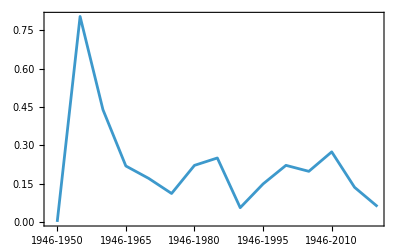
-Graphics-新規出現主要ディスクリプターの主要ディスクリプターに占める割合（%）

```mathematica
Labeled[ListPlot[mainMeSHgennewcomercount/mainMeSHflatcountAcm/.Indeterminate->0,Joined->True,PlotRange->Full,Frame->True,FrameTicks->{Automatic,{genticks,None}}],"新規出現主要ディスクリプターの主要ディスクリプターに占める割合（%）"]
```

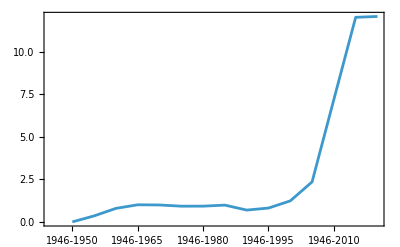
-Graphics-主要ディスクリプターの全出現ディスクリプターに占める割合（%）

```mathematica
Labeled[ListPlot[mainMeSHflatcountAcm/MeSHDesccountAcm*100,Joined->True,Frame->True,FrameTicks->{Automatic,{genticks,None}}],"主要ディスクリプターの全出現ディスクリプターに占める割合（%）"]
```

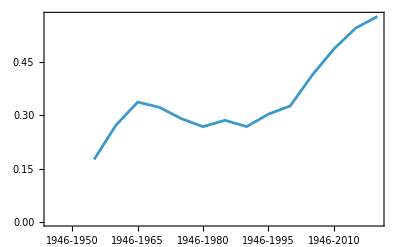

```mathematica
ListPlot[mainMeSHginiTbl,Joined->True,Frame->True,FrameTicks->{Automatic,{genticks,None}}]
```

```mathematica
Drop[{1,2,3},1]
```

{2,3}

```mathematica
genticks
```

{{1,1946-1950},{2,1946-1955},{3,1946-1960},{4,1946-1965},{5,1946-1970},{6,1946-1975},{7,1946-1980},{8,1946-1985},{9,1946-1990},{10,1946-1995},{11,1946-2000},{12,1946-2005},{13,1946-2010},{14,1946-2015},{15,1946-2020}}